### Two Term Wave Function

First we examine the properties of the following wave function ψ = 1/(√2)  (ψ_F χ_S + ψ_B χ_T )  where F and B denote the fermion and boson ground state in the spinless case and the S and T denote the singlet and triplet spin states

```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, B][x_,y_,t_]=Sign[y-x]Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity},Assumptions->{Im[x]==0,Im[y]==0}];
Subscript[ρ, B][x_,y_]=Subscript[ρ, F][x,y]-2*Sign[y-x]Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y},Assumptions->{Im[x]==0,Im[y]==0}]//FullSimplify;
Subscript[ns, F][x_]=2*Subscript[ρ, F][x,x];
(* This function is equal to the integral of Subscript[ϕ, B] Subscript[ϕ, F]= 2/π E^(-Subscript[x, 2]^2-x^2)(Subscript[x, 2]-x)Abs[Subscript[x, 2]-x] from -Inf to Inf*)
Subscript[ns, C][x_]=(ⅇ^(-2 x^2) (-2 x-ⅇ^(x^2) √π (1+2 x^2) Erf[x]))/π;
```

#### Real Space Density Profile

Here we calculate the real space density profile for two spinors with mixed wave function at t = 0

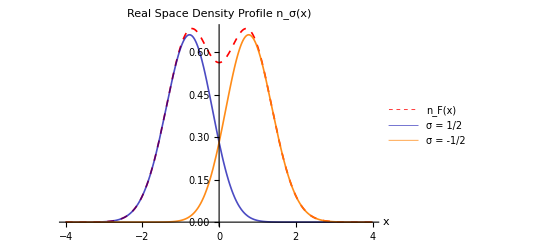

```mathematica
p1=Plot[{Subscript[ns, F][x],0.5*(Subscript[ns, F][x] + Subscript[ns, C][x]),0.5*(Subscript[ns, F][x] - Subscript[ns, C][x])},{x,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Real Space Density Profile n_σ(x)",Bold,16],PlotLegends->{"n_F(x)","σ = 1/2","σ = -1/2"},AxesLabel->{"x"}]
```

#### Momentum Space Density Profile

Here we plot the momentum space density profile for t = 0

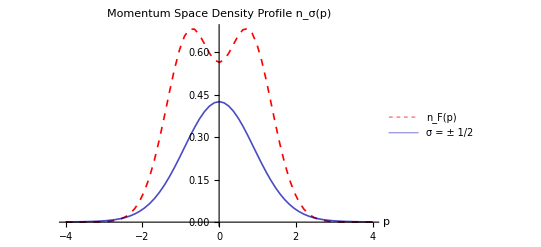

```mathematica
Subscript[n, F][p_] = 2/(2*π)*Integrate[E^(-I*p*(y-x))*Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞},Assumptions->Im[p]==0];
Subscript[n, B][p_] :=Subscript[n, B][p]= 2/(2π)*NIntegrate[Cos[p*(x-y)]Subscript[ρ, B][x,y],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->5,PrecisionGoal->5];
p2=Plot[{Subscript[n, F][p],0.25*(Subscript[n, F][p] + Subscript[n, B][p])},{p,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Momentum Space Density Profile n_σ(p)",Bold,16],PlotLegends->{"n_F(p)","σ = ± 1/2"},AxesLabel->{"p"},PlotPoints->5,MaxRecursion->4]
```

#### Momentum Space Density Profile - Dynamical Fermionization

Here we plot the momentum space density profile after the trapping potential has been turned off and t → ∞

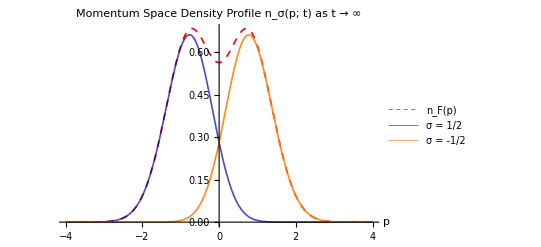

```mathematica
Subscript[n, C][p_]=(ⅇ^(-2 p^2) (-2 p-ⅇ^(p^2) √π (1+2 p^2) Erf[p]))/π;
pDF=Plot[{Subscript[n, F][p],0.5*(Subscript[n, F][p] + Subscript[n, C][p]),0.5*(Subscript[n, F][p] - Subscript[n, C][p])},{p,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Momentum Space Density Profile n_σ(p; t) as t → ∞",Bold,16],PlotLegends->{"n_F(p)","σ = 1/2","σ = -1/2"},AxesLabel->{"p"}]
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\MSDPMixedSpinorDF.png",pDF];
```

#### Time Evolution of RSDP

After Dyanmical Fermionization occurs, the momentum distribution for each particle is skewed either positive or negative dpending on the value of its spin
This should mean that in real space the particles are moving away from each other, one left and the other right

```mathematica
Manipulate[Plot[{Subscript[ns, F][x/b[t]]/b[t],0.5*(Subscript[ns, F][x/b[t]]+ Subscript[ns, C][x/b[t]])/b[t],0.5*(Subscript[ns, F][x/b[t]] - Subscript[ns, C][x/b[t]])/b[t]},{x,-8,8},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Real Space Density Profile n_σ(x;t)",Bold,16],PlotLegends->{"n_F(x;t)","σ = 1/2","σ = -1/2"},AxesLabel->{"x"},PlotRange->{0,.75}],{t,0,10}]
```

```mathematica
NumFrames=15;
Tdomain=Table[i*0.5,{i,0,NumFrames-1}];
frame[i_]:=Show[Plot[{Subscript[ns, F][x/b[t]]/b[t],0.5*(Subscript[ns, F][x/b[t]]+ Subscript[ns, C][x/b[t]])/b[t],0.5*(Subscript[ns, F][x/b[t]] - Subscript[ns, C][x/b[t]])/b[t]},{x,-8,8},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Real Space Density Profile n_σ(x;t)",Bold,16],PlotLegends->{"n_F(x;t)","σ = 1/2","σ = -1/2"},AxesLabel->{"x"},PlotRange->{0,.75}],
Graphics[Style[Text[StringForm["t = ``",Tdomain[[i]]],{3,0.7},{0,0}],17]]];
frames=Table[frame[i],{i,1,Length[Tdomain]}];
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\TimeEvolutionNS-RSDP.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .25];
```

Now let’s calculate the position of the density peaks as a function of time

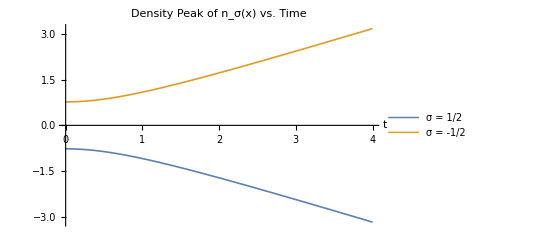

```mathematica
p3 = Plot[{ArgMax[{0.5*(Subscript[ns, F][x/b[t]]+ Subscript[ns, C][x/b[t]])/b[t],x<0},x],ArgMax[{0.5*(Subscript[ns, F][x/b[t]]- Subscript[ns, C][x/b[t]])/b[t],x>0},x]},{t,0,4},PlotStyle->{{Default,Thickness[.003]},{Default,Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Density Peak of n_σ(x) vs. Time",Bold,16],PlotLegends->{"σ = 1/2","σ = -1/2"},AxesLabel->{"t"}]
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\DensityPeaks.png",p3];
```

```mathematica
ArgMax[{0.5*(Subscript[ns, F][x]- Subscript[ns, C][x]),x>0},x]
Domain = Table[i/2.,{i,200,300}];
samp=ArgMax[{#,x>0},x]&/@(0.5*(Subscript[ns, F][x/b[t]]- Subscript[ns, C][x/b[t]])/b[t]/.({t-> #}& /@ Domain));
data=Thread[{Domain,samp}];
D[Fit[data, {1,x},x],x]
```

0.771242

0.771217

#### Time evolution of n_C(p)

We calculate the time evolution of n_C(p)

```mathematica
nc[p_,t_]:=nc[p,t]=b[t]/π^2 NIntegrate[Cos[p*b[t](x-y)+ b'[t]*b[t]/2 (y^2-x^2)] E^(-1/2*(y^2+x^2))(-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-Infinity,Infinity},{y,-Infinity, Infinity},AccuracyGoal->4];
Tdomain={0.0,0.05,0.1,0.25,0.5,0.75,1.0,1.5, 2.0,2.5, 3.0,5.0, 7.0,9.0};
(*Plot[nc[p,Tdomain[[#]]],{p,-4,4},PlotRange->{-0.8,.8},PlotPoints->5,MaxRecursion->4]&/@Table[i,{i,1,Length[Tdomain]}]*)
```

First we can create a gif of the time evolution

```mathematica
frame[i_]:=Show[Plot[{nc[p,Tdomain[[i]]],Subscript[n, C][p]},{p,-4,4},PlotStyle->{{Default,Thickness[0.003]}, {Red,Dashed,Thickness[0.003]}},TicksStyle->Directive["Label", 15], 
PlotRange->{-0.9,.9},PlotPoints->5,MaxRecursion->4,
PlotLabel->Style["Time Evolution of n_C(p;t)",Bold,20],AxesLabel->{Style["p",17]},
PlotLegends->{"n_C(p;t)","n_C(p; t → ∞)"}, ImageSize->Scaled[0.6]],
Graphics[Style[Text[StringForm["t = ``",Tdomain[[i]]],{3,0.7},{0,0}],17]]];
frames=Table[frame[i],{i,1,Length[Tdomain]}];
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\TimeEvolutionNC.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .25];
```

But it will also be convenient to create a still frame plot for printed media

```mathematica
?nc
```

Global`nc

nc[-4,0.]=6.21473×10^-11
 
nc[-4,0.05]=4.48517×10^-6
 
nc[-4,0.1]=8.49233×10^-6
 
nc[-4,0.25]=0.0000143932
 
nc[-4,0.5]=6.48895×10^-6
 
nc[-4,0.75]=5.49983×10^-7
 
nc[-4,1.]=1.1761×10^-6
 
nc[-4,1.5]=2.17744×10^-6
 
nc[-4,2.]=2.10012×10^-6
 
nc[-4,2.5]=2.09706×10^-6
 
nc[-4,3.]=2.10205×10^-6
 
nc[-4,5.]=2.09442×10^-6
 
nc[-4,7.]=6.63932×10^-7
 
nc[-4,9.]=0.0000218595
 
nc[-4.,0.]=-6.30595×10^-11
 
nc[-4.,0.05]=4.48671×10^-6
 
nc[-4.,0.1]=8.49471×10^-6
 
nc[-4.,0.25]=0.000014394
 
nc[-4.,0.5]=6.48877×10^-6
 
nc[-4.,0.75]=5.501×10^-7
 
nc[-4.,1.]=1.17605×10^-6
 
nc[-4.,1.5]=2.18079×10^-6
 
nc[-4.,2.]=2.1032×10^-6
 
nc[-4.,2.5]=2.09501×10^-6
 
nc[-4.,3.]=2.09457×10^-6
 
nc[-4.,5.]=2.0951×10^-6
 
nc[-4.,7.]=6.65581×10^-7
 
nc[-4.,9.]=0.0000218592
 
nc[-3.998,0.]=-1.27345×10^-10
 
nc[-3.998,0.05]=4.53204×10^-6
 
nc[-3.998,0.1]=8.58249×10^-6
 
nc[-3.998,0.25]=0.0000145566
 
nc[-3.998,0.5]=6.59301×10^-6
 
nc[-3.998,0.75]=5.74993×10^-7
 
nc[-3.998,1.]=1.19453×10^-6
 
nc[-3.998,1.5]=2.20866×10^-6
 
nc[-3.998,2.]=2.13314×10^-6
 
nc[-3.998,2.5]=2.12664×10^-6
 
nc[-3.998,3.]=2.51683×10^-6
 
nc[-3.998,5.]=2.12632×10^-6
 
nc[-3.998,7.]=-0.0000332753
 
nc[-3.998,9.]=0.0000218192
 
nc[-3.87977,0.]=-1.58919×10^-11
 
nc[-3.87977,0.05]=8.20196×10^-6
 
nc[-3.87977,0.1]=0.0000156341
 
nc[-3.87977,0.25]=0.0000278388
 
nc[-3.87977,0.5]=0.0000161229
 
nc[-3.87977,0.75]=3.51883×10^-6
 
nc[-3.87977,1.]=3.1011×10^-6
 
nc[-3.87977,1.5]=7.58175×10^-6
 
nc[-3.87977,2.]=5.12765×10^-6
 
nc[-3.87977,2.5]=5.09727×10^-6
 
nc[-3.87977,3.]=5.6736×10^-6
 
nc[-3.87977,5.]=0.0000194837
 
nc[-3.87977,7.]=0.0000202581
 
nc[-3.87977,9.]=-5.33412×10^-7
 
nc[-3.75955,0.]=6.2993×10^-11
 
nc[-3.75955,0.05]=0.0000146905
 
nc[-3.75955,0.1]=0.0000281669
 
nc[-3.75955,0.25]=0.0000524217
 
nc[-3.75955,0.5]=0.0000369575
 
nc[-3.75955,0.75]=0.000012376
 
nc[-3.75955,1.]=8.40258×10^-6
 
nc[-3.75955,1.5]=0.0000137722
 
nc[-3.75955,2.]=0.0000122183
 
nc[-3.75955,2.5]=0.0000120052
 
nc[-3.75955,3.]=0.0000120087
 
nc[-3.75955,5.]=0.0000120076
 
nc[-3.75955,7.]=0.0000119897
 
nc[-3.75955,9.]=0.000105098
 
nc[-3.63932,0.]=6.54909×10^-10
 
nc[-3.63932,0.05]=0.0000257738
 
nc[-3.63932,0.1]=0.0000496912
 
nc[-3.63932,0.25]=0.0000961654
 
nc[-3.63932,0.5]=0.0000795379
 
nc[-3.63932,0.75]=0.0000351149
 
nc[-3.63932,1.]=0.000022286
 
nc[-3.63932,1.5]=0.0000265494
 
nc[-3.63932,2.]=0.0000273824
 
nc[-3.63932,2.5]=0.0000274513
 
nc[-3.63932,3.]=0.0000274377
 
nc[-3.63932,5.]=0.000027449
 
nc[-3.63932,7.]=0.0000312582
 
nc[-3.63932,9.]=3.01852×10^-6
 
nc[-3.5191,0.]=8.0768×10^-11
 
nc[-3.5191,0.05]=0.0000443108
 
nc[-3.5191,0.1]=0.0000858308
 
nc[-3.5191,0.25]=0.000171948
 
nc[-3.5191,0.5]=0.000162383
 
nc[-3.5191,0.75]=0.0000878284
 
nc[-3.5191,1.]=0.0000563974
 
nc[-3.5191,1.5]=0.0000584984
 
nc[-3.5191,2.]=0.0000612733
 
nc[-3.5191,2.5]=0.0000608202
 
nc[-3.5191,3.]=0.0000608363
 
nc[-3.5191,5.]=0.0000608393
 
nc[-3.5191,7.]=0.0000567016
 
nc[-3.5191,9.]=0.000071829
 
nc[-3.39887,0.]=1.14849×10^-10
 
nc[-3.39887,0.05]=0.0000746224
 
nc[-3.39887,0.1]=0.000145167
 
nc[-3.39887,0.25]=0.000299816
 
nc[-3.39887,0.5]=0.000316556
 
nc[-3.39887,0.75]=0.000200758
 
nc[-3.39887,1.]=0.000134864
 
nc[-3.39887,1.5]=0.000125763
 
nc[-3.39887,2.]=0.00013015
 
nc[-3.39887,2.5]=0.000130648
 
nc[-3.39887,3.]=0.000130724
 
nc[-3.39887,5.]=0.000130741
 
nc[-3.39887,7.]=0.000385442
 
nc[-3.39887,9.]=0.000122721
 
nc[-3.27865,0.]=-3.01081×10^-10
 
nc[-3.27865,0.05]=0.000123082
 
nc[-3.27865,0.1]=0.000240362
 
nc[-3.27865,0.25]=0.000509958
 
nc[-3.27865,0.5]=0.000591949
 
nc[-3.27865,0.75]=0.000427302
 
nc[-3.27865,1.]=0.000304249
 
nc[-3.27865,1.5]=0.000264836
 
nc[-3.27865,2.]=0.000272294
 
nc[-3.27865,2.5]=0.000272025
 
nc[-3.27865,3.]=0.00027228
 
nc[-3.27865,5.]=0.000273015
 
nc[-3.27865,7.]=0.000310339
 
nc[-3.27865,9.]=0.000274075
 
nc[-3.15842,0.]=1.13746×10^-9
 
nc[-3.15842,0.05]=0.000198848
 
nc[-3.15842,0.1]=0.000389644
 
nc[-3.15842,0.25]=0.000846418
 
nc[-3.15842,0.5]=0.00106529
 
nc[-3.15842,0.75]=0.000856413
 
nc[-3.15842,1.]=0.000648562
 
nc[-3.15842,1.5]=0.000543288
 
nc[-3.15842,2.]=0.00054684
 
nc[-3.15842,2.5]=0.000549306
 
nc[-3.15842,3.]=0.000549705
 
nc[-3.15842,5.]=0.000549893
 
nc[-3.15842,7.]=0.000553401
 
nc[-3.15842,9.]=0.000537573
 
nc[-3.03819,0.]=1.57753×10^-9
 
nc[-3.03819,0.05]=0.000314627
 
nc[-3.03819,0.1]=0.000618361
 
nc[-3.03819,0.25]=0.0013712
 
nc[-3.03819,0.5]=0.00184957
 
nc[-3.03819,0.75]=0.0016283
 
nc[-3.03819,1.]=0.00130992
 
nc[-3.03819,1.5]=0.00108316
 
nc[-3.03819,2.]=0.00107305
 
nc[-3.03819,2.5]=0.00107438
 
nc[-3.03819,3.]=0.00107557
 
nc[-3.03819,5.]=0.00107594
 
nc[-3.03819,7.]=0.00107594
 
nc[-3.03819,9.]=0.00108289
 
nc[-2.91797,0.]=-3.33342×10^-9
 
nc[-2.91797,0.05]=0.000487487
 
nc[-2.91797,0.1]=0.000960588
 
nc[-2.91797,0.25]=0.00216863
 
nc[-2.91797,0.5]=0.00310406
 
nc[-2.91797,0.75]=0.00295209
 
nc[-2.91797,1.]=0.00251417
 
nc[-2.91797,1.5]=0.00209241
 
nc[-2.91797,2.]=0.00204034
 
nc[-2.91797,2.5]=0.0020387
 
nc[-2.91797,3.]=0.00203945
 
nc[-2.91797,5.]=0.0020398
 
nc[-2.91797,7.]=0.00203977
 
nc[-2.91797,9.]=0.00203976
 
nc[-2.79774,0.]=3.22596×10^-9
 
nc[-2.79774,0.05]=0.000739573
 
nc[-2.79774,0.1]=0.0014606
 
nc[-2.79774,0.25]=0.00334895
 
nc[-2.79774,0.5]=0.00504317
 
nc[-2.79774,0.75]=0.00512319
 
nc[-2.79774,1.]=0.0045985
 
nc[-2.79774,1.5]=0.00390579
 
nc[-2.79774,2.]=0.00376676
 
nc[-2.79774,2.5]=0.00374938
 
nc[-2.79774,3.]=0.00374714
 
nc[-2.79774,5.]=0.00374627
 
nc[-2.79774,7.]=0.00374614
 
nc[-2.79774,9.]=0.00374611
 
nc[-2.67752,0.]=3.49199×10^-9
 
nc[-2.67752,0.05]=0.00109842
 
nc[-2.67752,0.1]=0.00217355
 
nc[-2.67752,0.25]=0.00505044
 
nc[-2.67752,0.5]=0.00794198
 
nc[-2.67752,0.75]=0.00853577
 
nc[-2.67752,1.]=0.00803549
 
nc[-2.67752,1.5]=0.00703003
 
nc[-2.67752,2.]=0.00673883
 
nc[-2.67752,2.5]=0.00668225
 
nc[-2.67752,3.]=0.00666982
 
nc[-2.67752,5.]=0.00666401
 
nc[-2.67752,7.]=0.00666353
 
nc[-2.67752,9.]=0.00666344
 
nc[-2.55729,0.]=7.03675×10^-9
 
nc[-2.55729,0.05]=0.00159691
 
nc[-2.55729,0.1]=0.00316516
 
nc[-2.55729,0.25]=0.0074384
 
nc[-2.55729,0.5]=0.012135
 
nc[-2.55729,0.75]=0.013685
 
nc[-2.55729,1.]=0.013445
 
nc[-2.55729,1.5]=0.0121828
 
nc[-2.55729,2.]=0.0116683
 
nc[-2.55729,2.5]=0.0115349
 
nc[-2.55729,3.]=0.0114986
 
nc[-2.55729,5.]=0.0114789
 
nc[-2.55729,7.]=0.0114775
 
nc[-2.55729,9.]=0.0114783
 
nc[-2.43707,0.]=9.71039×10^-9
 
nc[-2.43707,0.05]=0.00227206
 
nc[-2.43707,0.1]=0.00450965
 
nc[-2.43707,0.25]=0.0106999
 
nc[-2.43707,0.5]=0.0180052
 
nc[-2.43707,0.75]=0.0211527
 
nc[-2.43707,1.]=0.0215832
 
nc[-2.43707,1.5]=0.0203086
 
nc[-2.43707,2.]=0.0195299
 
nc[-2.43707,2.5]=0.0192731
 
nc[-2.43707,3.]=0.0191916
 
nc[-2.43707,5.]=0.0191416
 
nc[-2.43707,7.]=0.0191381
 
nc[-2.43707,9.]=0.0191376
 
nc[-2.31684,0.]=3.53364×10^-9
 
nc[-2.31684,0.05]=0.00316296
 
nc[-2.31684,0.1]=0.00628528
 
nc[-2.31684,0.25]=0.0150325
 
nc[-2.31684,0.5]=0.0259593
 
nc[-2.31684,0.75]=0.0315696
 
nc[-2.31684,1.]=0.0332991
 
nc[-2.31684,1.5]=0.032552
 
nc[-2.31684,2.]=0.0315623
 
nc[-2.31684,2.5]=0.0311487
 
nc[-2.31684,3.]=0.0309967
 
nc[-2.31684,5.]=0.0308922
 
nc[-2.31684,7.]=0.0308847
 
nc[-2.31684,9.]=0.0308837
 
nc[-2.19662,0.]=3.96357×10^-8
 
nc[-2.19662,0.05]=0.00430723
 
nc[-2.19662,0.1]=0.00856734
 
nc[-2.19662,0.25]=0.0206255
 
nc[-2.19662,0.5]=0.036388
 
nc[-2.19662,0.75]=0.0455524
 
nc[-2.19662,1.]=0.0494503
 
nc[-2.19662,1.5]=0.0501666
 
nc[-2.19662,2.]=0.0492019
 
nc[-2.19662,2.5]=0.0486519
 
nc[-2.19662,3.]=0.0484155
 
nc[-2.19662,5.]=0.0482346
 
nc[-2.19662,7.]=0.0482216
 
nc[-2.19662,9.]=0.0482203
 
nc[-2.07639,0.]=1.15305×10^-8
 
nc[-2.07639,0.05]=0.00573595
 
nc[-2.07639,0.1]=0.0114179
 
nc[-2.07639,0.25]=0.0276348
 
nc[-2.07639,0.5]=0.0496111
 
nc[-2.07639,0.75]=0.063613
 
nc[-2.07639,1.]=0.070778
 
nc[-2.07639,1.5]=0.0743497
 
nc[-2.07639,2.]=0.0739261
 
nc[-2.07639,2.5]=0.0733775
 
nc[-2.07639,3.]=0.0730868
 
nc[-2.07639,5.]=0.0728349
 
nc[-2.07639,7.]=0.0728183
 
nc[-2.07639,9.]=0.0728184
 
nc[-1.94605,0.]=-4.13952×10^-8
 
nc[-1.94605,0.05]=0.0076268
 
nc[-1.94605,0.1]=0.0151918
 
nc[-1.94605,0.25]=0.0369352
 
nc[-1.94605,0.5]=0.0673075
 
nc[-1.94605,0.75]=0.0881378
 
nc[-1.94605,1.]=0.100281
 
nc[-1.94605,1.5]=0.109029
 
nc[-1.94605,2.]=0.110187
 
nc[-1.94605,2.5]=0.110019
 
nc[-1.94605,3.]=0.109808
 
nc[-1.94605,5.]=0.10958
 
nc[-1.94605,7.]=0.109576
 
nc[-1.94605,9.]=0.109584
 
nc[-1.81571,0.]=3.39153×10^-8
 
nc[-1.81571,0.05]=0.00986874
 
nc[-1.81571,0.1]=0.0196673
 
nc[-1.81571,0.25]=0.0479792
 
nc[-1.81571,0.5]=0.0884378
 
nc[-1.81571,0.75]=0.117732
 
nc[-1.81571,1.]=0.136409
 
nc[-1.81571,1.5]=0.152871
 
nc[-1.81571,2.]=0.157099
 
nc[-1.81571,2.5]=0.158023
 
nc[-1.81571,3.]=0.158212
 
nc[-1.81571,5.]=0.158316
 
nc[-1.81571,7.]=0.158376
 
nc[-1.81571,9.]=0.158411
 
nc[-1.68538,0.]=-1.04498×10^-8
 
nc[-1.68538,0.05]=0.0124189
 
nc[-1.68538,0.1]=0.0247582
 
nc[-1.68538,0.25]=0.0605468
 
nc[-1.68538,0.5]=0.112543
 
nc[-1.68538,0.75]=0.151707
 
nc[-1.68538,1.]=0.178321
 
nc[-1.68538,1.5]=0.205083
 
nc[-1.68538,2.]=0.214205
 
nc[-1.68538,2.5]=0.217264
 
nc[-1.68538,3.]=0.218407
 
nc[-1.68538,5.]=0.219479
 
nc[-1.68538,7.]=0.219724
 
nc[-1.68538,9.]=0.219829
 
nc[-1.55504,0.]=-2.17386×10^-8
 
nc[-1.55504,0.05]=0.015186
 
nc[-1.55504,0.1]=0.0302818
 
nc[-1.55504,0.25]=0.0741772
 
nc[-1.55504,0.5]=0.138683
 
nc[-1.55504,0.75]=0.188651
 
nc[-1.55504,1.]=0.224195
 
nc[-1.55504,1.5]=0.263412
 
nc[-1.55504,2.]=0.279301
 
nc[-1.55504,2.5]=0.285767
 
nc[-1.55504,3.]=0.288636
 
nc[-1.55504,5.]=0.291724
 
nc[-1.55504,7.]=0.29238
 
nc[-1.55504,9.]=0.292637
 
nc[-1.4247,0.]=1.00562×10^-8
 
nc[-1.4247,0.05]=0.0180257
 
nc[-1.4247,0.1]=0.0359493
 
nc[-1.4247,0.25]=0.0881475
 
nc[-1.4247,0.5]=0.16541
 
nc[-1.4247,0.75]=0.226399
 
nc[-1.4247,1.]=0.271208
 
nc[-1.4247,1.5]=0.324096
 
nc[-1.4247,2.]=0.34826
 
nc[-1.4247,2.5]=0.359394
 
nc[-1.4247,3.]=0.364879
 
nc[-1.4247,5.]=0.371409
 
nc[-1.4247,7.]=0.372832
 
nc[-1.4247,9.]=0.373376
 
nc[-1.29436,0.]=5.70339×10^-9
 
nc[-1.29436,0.05]=0.0207415
 
nc[-1.29436,0.1]=0.0413683
 
nc[-1.29436,0.25]=0.101482
 
nc[-1.29436,0.5]=0.190803
 
nc[-1.29436,0.75]=0.26213
 
nc[-1.29436,1.]=0.315698
 
nc[-1.29436,1.5]=0.382101
 
nc[-1.29436,2.]=0.415248
 
nc[-1.29436,2.5]=0.431978
 
nc[-1.29436,3.]=0.440879
 
nc[-1.29436,5.]=0.452437
 
nc[-1.29436,7.]=0.455116
 
nc[-1.29436,9.]=0.45614
 
nc[-1.16402,0.]=3.33617×10^-9
 
nc[-1.16402,0.05]=0.0230951
 
nc[-1.16402,0.1]=0.0460625
 
nc[-1.16402,0.25]=0.113004
 
nc[-1.16402,0.5]=0.212588
 
nc[-1.16402,0.75]=0.292572
 
nc[-1.16402,1.]=0.35347
 
nc[-1.16402,1.5]=0.431642
 
nc[-1.16402,2.]=0.473346
 
nc[-1.16402,2.5]=0.495938
 
nc[-1.16402,3.]=0.508726
 
nc[-1.16402,5.]=0.526683
 
nc[-1.16402,7.]=0.531144
 
nc[-1.16402,9.]=0.532877
 
nc[-1.03369,0.]=-8.73496×10^-9
 
nc[-1.03369,0.05]=0.0248241
 
nc[-1.03369,0.1]=0.0495091
 
nc[-1.03369,0.25]=0.12143
 
nc[-1.03369,0.5]=0.228337
 
nc[-1.03369,0.75]=0.314313
 
nc[-1.03369,1.]=0.380244
 
nc[-1.03369,1.5]=0.466903
 
nc[-1.03369,2.]=0.515495
 
nc[-1.03369,2.5]=0.543341
 
nc[-1.03369,3.]=0.559932
 
nc[-1.03369,5.]=0.58495
 
nc[-1.03369,7.]=0.591632
 
nc[-1.03369,9.]=0.594293
 
nc[-0.903348,0.]=2.39627×10^-8
 
nc[-0.903348,0.05]=0.0256701
 
nc[-0.903348,0.1]=0.0511928
 
nc[-0.903348,0.25]=0.125504
 
nc[-0.903348,0.5]=0.235722
 
nc[-0.903348,0.75]=0.324182
 
nc[-0.903348,1.]=0.392161
 
nc[-0.903348,1.5]=0.482817
 
nc[-0.903348,2.]=0.535541
 
nc[-0.903348,2.5]=0.567141
 
nc[-0.903348,3.]=0.586797
 
nc[-0.903348,5.]=0.618417
 
nc[-0.903348,7.]=0.627488
 
nc[-0.903348,9.]=0.631203
 
nc[-0.77301,0.]=5.77512×10^-8
 
nc[-0.77301,0.05]=0.0254101
 
nc[-0.77301,0.1]=0.0506699
 
nc[-0.77301,0.25]=0.124152
 
nc[-0.77301,0.5]=0.232812
 
nc[-0.77301,0.75]=0.319647
 
nc[-0.77301,1.]=0.386269
 
nc[-0.77301,1.5]=0.475762
 
nc[-0.77301,2.]=0.529164
 
nc[-0.77301,2.5]=0.562324
 
nc[-0.77301,3.]=0.583707
 
nc[-0.77301,5.]=0.620167
 
nc[-0.77301,7.]=0.631359
 
nc[-0.77301,9.]=0.63608
 
nc[-0.642672,0.]=-1.7345×10^-8
 
nc[-0.642672,0.05]=0.0238902
 
nc[-0.642672,0.1]=0.0476349
 
nc[-0.642672,0.25]=0.116646
 
nc[-0.642672,0.5]=0.218346
 
nc[-0.642672,0.75]=0.29917
 
nc[-0.642672,1.]=0.360926
 
nc[-0.642672,1.5]=0.44403
 
nc[-0.642672,2.]=0.494462
 
nc[-0.642672,2.5]=0.526648
 
nc[-0.642672,3.]=0.54803
 
nc[-0.642672,5.]=0.58641
 
nc[-0.642672,7.]=0.598945
 
nc[-0.642672,9.]=0.604386
 
nc[-0.512334,0.]=-9.87151×10^-9
 
nc[-0.512334,0.05]=0.0210551
 
nc[-0.512334,0.1]=0.0419785
 
nc[-0.512334,0.25]=0.102735
 
nc[-0.512334,0.5]=0.19197
 
nc[-0.512334,0.75]=0.262471
 
nc[-0.512334,1.]=0.316048
 
nc[-0.512334,1.5]=0.388008
 
nc[-0.512334,2.]=0.432114
 
nc[-0.512334,2.5]=0.460846
 
nc[-0.512334,3.]=0.480395
 
nc[-0.512334,5.]=0.517064
 
nc[-0.512334,7.]=0.529708
 
nc[-0.512334,9.]=0.53534
 
nc[-0.381995,0.]=2.06586×10^-9
 
nc[-0.381995,0.05]=0.0169669
 
nc[-0.381995,0.1]=0.0338249
 
nc[-0.381995,0.25]=0.0827399
 
nc[-0.381995,0.5]=0.154369
 
nc[-0.381995,0.75]=0.210651
 
nc[-0.381995,1.]=0.253185
 
nc[-0.381995,1.5]=0.310093
 
nc[-0.381995,2.]=0.345148
 
nc[-0.381995,2.5]=0.368319
 
nc[-0.381995,3.]=0.384377
 
nc[-0.381995,5.]=0.41559
 
nc[-0.381995,7.]=0.426845
 
nc[-0.381995,9.]=0.431969
 
nc[-0.251657,0.]=-3.08223×10^-9
 
nc[-0.251657,0.05]=0.0118102
 
nc[-0.251657,0.1]=0.0235434
 
nc[-0.251657,0.25]=0.0575678
 
nc[-0.251657,0.5]=0.107277
 
nc[-0.251657,0.75]=0.146166
 
nc[-0.251657,1.]=0.175417
 
nc[-0.251657,1.5]=0.21439
 
nc[-0.251657,2.]=0.238442
 
nc[-0.251657,2.5]=0.254493
 
nc[-0.251657,3.]=0.265762
 
nc[-0.251657,5.]=0.28825
 
nc[-0.251657,7.]=0.296634
 
nc[-0.251657,9.]=0.300514
 
nc[-0.121319,0.]=-5.8919×10^-9
 
nc[-0.121319,0.05]=0.00588092
 
nc[-0.121319,0.1]=0.0117231
 
nc[-0.121319,0.25]=0.0286584
 
nc[-0.121319,0.5]=0.053365
 
nc[-0.121319,0.75]=0.0726405
 
nc[-0.121319,1.]=0.0870936
 
nc[-0.121319,1.5]=0.106292
 
nc[-0.121319,2.]=0.118145
 
nc[-0.121319,2.5]=0.126097
 
nc[-0.121319,3.]=0.131723
 
nc[-0.121319,5.]=0.143129
 
nc[-0.121319,7.]=0.147469
 
nc[-0.121319,9.]=0.149498
 
nc[0.,0.]=0.
 
nc[0.,0.1]=1.87779×10^-9
 
nc[0.00901899,0.]=1.35321×10^-9
 
nc[0.00901899,0.05]=-0.000441472
 
nc[0.00901899,0.1]=-0.000880057
 
nc[0.00901899,0.25]=-0.0021512
 
nc[0.00901899,0.5]=-0.00400487
 
nc[0.00901899,0.75]=-0.00544978
 
nc[0.00901899,1.]=-0.00653206
 
nc[0.00901899,1.5]=-0.00796848
 
nc[0.00901899,2.]=-0.00885521
 
nc[0.00901899,2.5]=-0.00945103
 
nc[0.00901899,3.]=-0.00987348
 
nc[0.00901899,5.]=-0.0107343
 
nc[0.00901899,7.]=-0.0110639
 
nc[0.00901899,9.]=-0.0112185
 
nc[0.13072,0.]=-2.10331×10^-8
 
nc[0.13072,0.05]=-0.00632663
 
nc[0.13072,0.1]=-0.0126116
 
nc[0.13072,0.25]=-0.0308308
 
nc[0.13072,0.5]=-0.0574123
 
nc[0.13072,0.75]=-0.0781535
 
nc[0.13072,1.]=-0.0937079
 
nc[0.13072,1.5]=-0.114373
 
nc[0.13072,2.]=-0.127131
 
nc[0.13072,2.5]=-0.135688
 
nc[0.13072,3.]=-0.14174
 
nc[0.13072,5.]=-0.154
 
nc[0.13072,7.]=-0.15866
 
nc[0.13072,9.]=-0.160838
 
nc[0.252421,0.]=-2.51589×10^-8
 
nc[0.252421,0.05]=-0.011843
 
nc[0.252421,0.1]=-0.0236087
 
nc[0.252421,0.25]=-0.0577278
 
nc[0.252421,0.5]=-0.107576
 
nc[0.252421,0.75]=-0.146574
 
nc[0.252421,1.]=-0.175908
 
nc[0.252421,1.5]=-0.214992
 
nc[0.252421,2.]=-0.239113
 
nc[0.252421,2.5]=-0.255209
 
nc[0.252421,3.]=-0.266509
 
nc[0.252421,5.]=-0.289056
 
nc[0.252421,7.]=-0.297461
 
nc[0.252421,9.]=-0.30135
 
nc[0.374122,0.]=-1.34416×10^-8
 
nc[0.374122,0.05]=-0.0166832
 
nc[0.374122,0.1]=-0.0332593
 
nc[0.374122,0.25]=-0.0813541
 
nc[0.374122,0.5]=-0.151771
 
nc[0.374122,0.75]=-0.207084
 
nc[0.374122,1.]=-0.248872
 
nc[0.374122,1.5]=-0.304768
 
nc[0.374122,2.]=-0.339205
 
nc[0.374122,2.5]=-0.361984
 
nc[0.374122,3.]=-0.377786
 
nc[0.374122,5.]=-0.408557
 
nc[0.374122,7.]=-0.419679
 
nc[0.374122,9.]=-0.424749
 
nc[0.495822,0.]=-2.99646×10^-8
 
nc[0.495822,0.05]=-0.0206039
 
nc[0.495822,0.1]=-0.0410783
 
nc[0.495822,0.25]=-0.100526
 
nc[0.495822,0.5]=-0.187802
 
nc[0.495822,0.75]=-0.256705
 
nc[0.495822,1.]=-0.309029
 
nc[0.495822,1.5]=-0.379278
 
nc[0.495822,2.]=-0.422373
 
nc[0.495822,2.5]=-0.450507
 
nc[0.495822,3.]=-0.4697
 
nc[0.495822,5.]=-0.50588
 
nc[0.495822,7.]=-0.518434
 
nc[0.495822,9.]=-0.524042
 
nc[0.617523,0.]=-1.68215×10^-8
 
nc[0.617523,0.05]=-0.0234454
 
nc[0.617523,0.1]=-0.0467472
 
nc[0.617523,0.25]=-0.114459
 
nc[0.617523,0.5]=-0.214178
 
nc[0.617523,0.75]=-0.293338
 
nc[0.617523,1.]=-0.353762
 
nc[0.617523,1.5]=-0.435064
 
nc[0.617523,2.]=-0.484521
 
nc[0.617523,2.5]=-0.516226
 
nc[0.617523,3.]=-0.537395
 
nc[0.617523,5.]=-0.57574
 
nc[0.617523,7.]=-0.588404
 
nc[0.617523,9.]=-0.593929
 
nc[0.739224,0.]=4.73497×10^-8
 
nc[0.739224,0.05]=-0.0251412
 
nc[0.739224,0.1]=-0.0501327
 
nc[0.739224,0.25]=-0.122817
 
nc[0.739224,0.5]=-0.230203
 
nc[0.739224,0.75]=-0.315904
 
nc[0.739224,1.]=-0.381599
 
nc[0.739224,1.5]=-0.469928
 
nc[0.739224,2.]=-0.522906
 
nc[0.739224,2.5]=-0.556061
 
nc[0.739224,3.]=-0.577619
 
nc[0.739224,5.]=-0.614896
 
nc[0.739224,7.]=-0.626531
 
nc[0.739224,9.]=-0.631476
 
nc[0.860925,0.]=1.20087×10^-8
 
nc[0.860925,0.05]=-0.025716
 
nc[0.860925,0.1]=-0.0512831
 
nc[0.860925,0.25]=-0.125703
 
nc[0.860925,0.5]=-0.235982
 
nc[0.860925,0.75]=-0.324384
 
nc[0.860925,1.]=-0.392307
 
nc[0.860925,1.5]=-0.483167
 
nc[0.860925,2.]=-0.536511
 
nc[0.860925,2.5]=-0.568884
 
nc[0.860925,3.]=-0.589273
 
nc[0.860925,5.]=-0.622725
 
nc[0.860925,7.]=-0.632539
 
nc[0.860925,9.]=-0.636598
 
nc[0.982626,0.]=-6.91457×10^-8
 
nc[0.982626,0.05]=-0.0252742
 
nc[0.982626,0.1]=-0.0504056
 
nc[0.982626,0.25]=-0.123609
 
nc[0.982626,0.5]=-0.232345
 
nc[0.982626,0.75]=-0.319751
 
nc[0.982626,1.]=-0.386871
 
nc[0.982626,1.5]=-0.475681
 
nc[0.982626,2.]=-0.526269
 
nc[0.982626,2.5]=-0.555809
 
nc[0.982626,3.]=-0.573725
 
nc[0.982626,5.]=-0.601456
 
nc[0.982626,7.]=-0.609075
 
nc[0.982626,9.]=-0.612141
 
nc[1.10433,0.]=-1.6933×10^-8
 
nc[1.10433,0.05]=-0.0239806
 
nc[1.10433,0.1]=-0.0478279
 
nc[1.10433,0.25]=-0.117325
 
nc[1.10433,0.5]=-0.220696
 
nc[1.10433,0.75]=-0.303811
 
nc[1.10433,1.]=-0.367346
 
nc[1.10433,1.5]=-0.449897
 
nc[1.10433,2.]=-0.495035
 
nc[1.10433,2.5]=-0.520165
 
nc[1.10433,3.]=-0.534744
 
nc[1.10433,5.]=-0.555913
 
nc[1.10433,7.]=-0.561348
 
nc[1.10433,9.]=-0.563483
 
nc[1.22603,0.]=-1.63204×10^-8
 
nc[1.22603,0.05]=-0.022037
 
nc[1.22603,0.1]=-0.0439523
 
nc[1.22603,0.25]=-0.107829
 
nc[1.22603,0.5]=-0.202827
 
nc[1.22603,0.75]=-0.278967
 
nc[1.22603,1.]=-0.336614
 
nc[1.22603,1.5]=-0.409508
 
nc[1.22603,2.]=-0.447273
 
nc[1.22603,2.5]=-0.467096
 
nc[1.22603,3.]=-0.478007
 
nc[1.22603,5.]=-0.492783
 
nc[1.22603,7.]=-0.496332
 
nc[1.22603,9.]=-0.497698
 
nc[1.34773,0.]=3.27193×10^-8
 
nc[1.34773,0.05]=-0.019659
 
nc[1.34773,0.1]=-0.0392086
 
nc[1.34773,0.25]=-0.0961709
 
nc[1.34773,0.5]=-0.180707
 
nc[1.34773,0.75]=-0.247947
 
nc[1.34773,1.]=-0.298049
 
nc[1.34773,1.5]=-0.359037
 
nc[1.34773,2.]=-0.388487
 
nc[1.34773,2.5]=-0.40285
 
nc[1.34773,3.]=-0.410271
 
nc[1.34773,5.]=-0.419581
 
nc[1.34773,7.]=-0.421683
 
nc[1.34773,9.]=-0.422484
 
nc[1.46943,0.]=-3.74495×10^-9
 
nc[1.46943,0.05]=-0.0170542
 
nc[1.46943,0.1]=-0.0340106
 
nc[1.46943,0.25]=-0.0833708
 
nc[1.46943,0.5]=-0.156283
 
nc[1.46943,0.75]=-0.213518
 
nc[1.46943,1.]=-0.255159
 
nc[1.46943,1.5]=-0.303296
 
nc[1.46943,2.]=-0.324493
 
nc[1.46943,2.5]=-0.333896
 
nc[1.46943,3.]=-0.338383
 
nc[1.46943,5.]=-0.343553
 
nc[1.46943,7.]=-0.344665
 
nc[1.46943,9.]=-0.345092
 
nc[1.59113,0.]=-5.22832×10^-9
 
nc[1.59113,0.05]=-0.0144053
 
nc[1.59113,0.1]=-0.0287236
 
nc[1.59113,0.25]=-0.0703332
 
nc[1.59113,0.5]=-0.131315
 
nc[1.59113,0.75]=-0.178235
 
nc[1.59113,1.]=-0.21124
 
nc[1.59113,1.5]=-0.246838
 
nc[1.59113,2.]=-0.260679
 
nc[1.59113,2.5]=-0.266068
 
nc[1.59113,3.]=-0.268373
 
nc[1.59113,5.]=-0.270774
 
nc[1.59113,7.]=-0.271285
 
nc[1.59113,9.]=-0.271489
 
nc[1.71283,0.]=2.27281×10^-9
 
nc[1.71283,0.05]=-0.0118598
 
nc[1.71283,0.1]=-0.0236422
 
nc[1.71283,0.25]=-0.0577918
 
nc[1.71283,0.5]=-0.107257
 
nc[1.71283,0.75]=-0.144245
 
nc[1.71283,1.]=-0.169087
 
nc[1.71283,1.5]=-0.193478
 
nc[1.71283,2.]=-0.20141
 
nc[1.71283,2.5]=-0.203918
 
nc[1.71283,3.]=-0.204802
 
nc[1.71283,5.]=-0.205598
 
nc[1.71283,7.]=-0.205789
 
nc[1.71283,9.]=-0.205874
 
nc[1.83453,0.]=1.17443×10^-8
 
nc[1.83453,0.05]=-0.00952452
 
nc[1.83453,0.1]=-0.0189801
 
nc[1.83453,0.25]=-0.0462831
 
nc[1.83453,0.5]=-0.0851877
 
nc[1.83453,0.75]=-0.113165
 
nc[1.83453,1.]=-0.130805
 
nc[1.83453,1.5]=-0.145991
 
nc[1.83453,2.]=-0.149668
 
nc[1.83453,2.5]=-0.150378
 
nc[1.83453,3.]=-0.15048
 
nc[1.83453,5.]=-0.150506
 
nc[1.83453,7.]=-0.150551
 
nc[1.83453,9.]=-0.150581
 
nc[1.95623,0.]=7.14988×10^-9
 
nc[1.95623,0.05]=-0.00746615
 
nc[1.95623,0.1]=-0.0148713
 
nc[1.95623,0.25]=-0.0361446
 
nc[1.95623,0.5]=-0.0657987
 
nc[1.95623,0.75]=-0.0860355
 
nc[1.95623,1.]=-0.0977334
 
nc[1.95623,1.5]=-0.105989
 
nc[1.95623,2.]=-0.106976
 
nc[1.95623,2.5]=-0.106757
 
nc[1.95623,3.]=-0.106531
 
nc[1.95623,5.]=-0.106293
 
nc[1.95623,7.]=-0.106287
 
nc[1.95623,9.]=-0.106294
 
nc[2.08397,0.]=8.94783×10^-9
 
nc[2.08397,0.05]=-0.00563709
 
nc[2.08397,0.1]=-0.0112207
 
nc[2.08397,0.25]=-0.0271491
 
nc[2.08397,0.5]=-0.0486909
 
nc[2.08397,0.75]=-0.0623472
 
nc[2.08397,1.]=-0.0692702
 
nc[2.08397,1.5]=-0.0726122
 
nc[2.08397,2.]=-0.0721327
 
nc[2.08397,2.5]=-0.0715767
 
nc[2.08397,3.]=-0.0712871
 
nc[2.08397,5.]=-0.0710383
 
nc[2.08397,7.]=-0.0710217
 
nc[2.08397,9.]=-0.0710216
 
nc[2.2117,0.]=1.43914×10^-12
 
nc[2.2117,0.05]=-0.0041486
 
nc[2.2117,0.1]=-0.00825086
 
nc[2.2117,0.25]=-0.0198487
 
nc[2.2117,0.5]=-0.0349316
 
nc[2.2117,0.75]=-0.0435829
 
nc[2.2117,1.]=-0.0471528
 
nc[2.2117,1.5]=-0.0476187
 
nc[2.2117,2.]=-0.0466292
 
nc[2.2117,2.5]=-0.0460919
 
nc[2.2117,3.]=-0.0458657
 
nc[2.2117,5.]=-0.0456951
 
nc[2.2117,7.]=-0.0456828
 
nc[2.2117,9.]=-0.0456815
 
nc[2.33944,0.]=-3.33869×10^-9
 
nc[2.33944,0.05]=-0.00297724
 
nc[2.33944,0.1]=-0.00591507
 
nc[2.33944,0.25]=-0.0141274
 
nc[2.33944,0.5]=-0.0242866
 
nc[2.33944,0.75]=-0.0293574
 
nc[2.33944,1.]=-0.0307838
 
nc[2.33944,1.5]=-0.0298793
 
nc[2.33944,2.]=-0.0289181
 
nc[2.33944,2.5]=-0.0285348
 
nc[2.33944,3.]=-0.0283977
 
nc[2.33944,5.]=-0.0283054
 
nc[2.33944,7.]=-0.0282989
 
nc[2.33944,9.]=-0.0282999
 
nc[2.46717,0.]=2.01038×10^-9
 
nc[2.46717,0.05]=-0.00208426
 
nc[2.46717,0.1]=-0.00413556
 
nc[2.46717,0.25]=-0.00979042
 
nc[2.46717,0.5]=-0.0163556
 
nc[2.46717,0.75]=-0.0190308
 
nc[2.46717,1.]=-0.0192436
 
nc[2.46717,1.5]=-0.0179349
 
nc[2.46717,2.]=-0.0172224
 
nc[2.46717,2.5]=-0.0170005
 
nc[2.46717,3.]=-0.0169329
 
nc[2.46717,5.]=-0.0168925
 
nc[2.46717,7.]=-0.0168897
 
nc[2.46717,9.]=-0.0167826
 
nc[2.59491,0.]=5.80444×10^-9
 
nc[2.59491,0.05]=-0.00142375
 
nc[2.59491,0.1]=-0.00282059
 
nc[2.59491,0.25]=-0.00660649
 
nc[2.59491,0.5]=-0.0106616
 
nc[2.59491,0.75]=-0.0118535
 
nc[2.59491,1.]=-0.0114971
 
nc[2.59491,1.5]=-0.0102999
 
nc[2.59491,2.]=-0.00986204
 
nc[2.59491,2.5]=-0.00975901
 
nc[2.59491,3.]=-0.00973021
 
nc[2.59491,5.]=-0.00971664
 
nc[2.59491,7.]=-0.00971562
 
nc[2.59491,9.]=-0.00960508
 
nc[2.72264,0.]=5.39049×10^-9
 
nc[2.72264,0.05]=-0.000949241
 
nc[2.72264,0.1]=-0.00187702
 
nc[2.72264,0.25]=-0.00434074
 
nc[2.72264,0.5]=-0.0067214
 
nc[2.72264,0.75]=-0.00708002
 
nc[2.72264,1.]=-0.00655072
 
nc[2.72264,1.5]=-0.00566306
 
nc[2.72264,2.]=-0.00543752
 
nc[2.72264,2.5]=-0.0053995
 
nc[2.72264,3.]=-0.00539191
 
nc[2.72264,5.]=-0.00538865
 
nc[2.72264,7.]=-0.00538835
 
nc[2.72264,9.]=-0.00541729
 
nc[2.85038,0.]=3.78395×10^-9
 
nc[2.85038,0.05]=-0.000617812
 
nc[2.85038,0.1]=-0.00121899
 
nc[2.85038,0.25]=-0.00277687
 
nc[2.85038,0.5]=-0.00409375
 
nc[2.85038,0.75]=-0.00404549
 
nc[2.85038,1.]=-0.0035507
 
nc[2.85038,1.5]=-0.00298491
 
nc[2.85038,2.]=-0.0028909
 
nc[2.85038,2.5]=-0.00288247
 
nc[2.85038,3.]=-0.0028822
 
nc[2.85038,5.]=-0.00288213
 
nc[2.85038,7.]=-0.00288206
 
nc[2.85038,9.]=-0.00288204
 
nc[2.97812,0.]=1.00928×10^-9
 
nc[2.97812,0.05]=-0.000392616
 
nc[2.97812,0.1]=-0.000772685
 
nc[2.97812,0.25]=-0.00172937
 
nc[2.97812,0.5]=-0.00240567
 
nc[2.97812,0.75]=-0.00220458
 
nc[2.97812,1.]=-0.0018257
 
nc[2.97812,1.5]=-0.00151141
 
nc[2.97812,2.]=-0.00148431
 
nc[2.97812,2.5]=-0.00148491
 
nc[2.97812,3.]=-0.00148664
 
nc[2.97812,5.]=-0.00148706
 
nc[2.97812,7.]=-0.00148705
 
nc[2.97812,9.]=-0.00148214
 
nc[3.10585,0.]=2.58642×10^-9
 
nc[3.10585,0.05]=-0.000243656
 
nc[3.10585,0.1]=-0.00047809
 
nc[3.10585,0.25]=-0.0010483
 
nc[3.10585,0.5]=-0.00136175
 
nc[3.10585,0.75]=-0.00114122
 
nc[3.10585,1.]=-0.000887665
 
nc[3.10585,1.5]=-0.00073733
 
nc[3.10585,2.]=-0.000738905
 
nc[3.10585,2.5]=-0.000739327
 
nc[3.10585,3.]=-0.00074006
 
nc[3.10585,5.]=-0.000742972
 
nc[3.10585,7.]=-0.000740331
 
nc[3.10585,9.]=-0.000809753
 
nc[3.23359,0.]=1.02363×10^-9
 
nc[3.23359,0.05]=-0.000147681
 
nc[3.23359,0.1]=-0.000288795
 
nc[3.23359,0.25]=-0.000618374
 
nc[3.23359,0.5]=-0.000740989
 
nc[3.23359,0.75]=-0.000558162
 
nc[3.23359,1.]=-0.000406687
 
nc[3.23359,1.5]=-0.000347774
 
nc[3.23359,2.]=-0.000353558
 
nc[3.23359,2.5]=-0.000355239
 
nc[3.23359,3.]=-0.000355602
 
nc[3.23359,5.]=-0.000355707
 
nc[3.23359,7.]=-0.000355707
 
nc[3.23359,9.]=-0.000367344
 
nc[3.36132,0.]=3.63061×10^-10
 
nc[3.36132,0.05]=-0.0000874303
 
nc[3.36132,0.1]=-0.000170315
 
nc[3.36132,0.25]=-0.000354859
 
nc[3.36132,0.5]=-0.000386559
 
nc[3.36132,0.75]=-0.000255968
 
nc[3.36132,1.]=-0.000174968
 
nc[3.36132,1.5]=-0.000159141
 
nc[3.36132,2.]=-0.000163994
 
nc[3.36132,2.5]=-0.000164826
 
nc[3.36132,3.]=-0.000164908
 
nc[3.36132,5.]=-0.000164973
 
nc[3.36132,7.]=-0.000574271
 
nc[3.36132,9.]=-0.000165016
 
nc[3.48906,0.]=-2.04897×10^-10
 
nc[3.48906,0.05]=-0.0000505683
 
nc[3.48906,0.1]=-0.0000980654
 
nc[3.48906,0.25]=-0.000198038
 
nc[3.48906,0.5]=-0.000192649
 
nc[3.48906,0.75]=-0.000108796
 
nc[3.48906,1.]=-0.0000705077
 
nc[3.48906,1.5]=-0.0000713628
 
nc[3.48906,2.]=-0.0000735372
 
nc[3.48906,2.5]=-0.000073842
 
nc[3.48906,3.]=-0.0000738632
 
nc[3.48906,5.]=-0.0000738692
 
nc[3.48906,7.]=0.000949412
 
nc[3.48906,9.]=-0.0000869158
 
nc[3.61679,0.]=4.88389×10^-11
 
nc[3.61679,0.05]=-0.0000285817
 
nc[3.61679,0.1]=-0.0000551379
 
nc[3.61679,0.25]=-0.000107438
 
nc[3.61679,0.5]=-0.0000912652
 
nc[3.61679,0.75]=-0.0000420376
 
nc[3.61679,1.]=-0.000026628
 
nc[3.61679,1.5]=-0.000030795
 
nc[3.61679,2.]=-0.0000320045
 
nc[3.61679,2.5]=-0.0000319396
 
nc[3.61679,3.]=-0.0000319289
 
nc[3.61679,5.]=-0.0000319373
 
nc[3.61679,7.]=-0.0000319267
 
nc[3.61679,9.]=-0.0000495281
 
nc[3.74453,0.]=-1.04695×10^-10
 
nc[3.74453,0.05]=-0.0000157793
 
nc[3.74453,0.1]=-0.0000302717
 
nc[3.74453,0.25]=-0.0000566281
 
nc[3.74453,0.5]=-0.0000408011
 
nc[3.74453,0.75]=-0.0000142258
 
nc[3.74453,1.]=-9.50944×10^-6
 
nc[3.74453,1.5]=-0.0000148317
 
nc[3.74453,2.]=-0.0000135431
 
nc[3.74453,2.5]=-0.0000133385
 
nc[3.74453,3.]=-0.000013336
 
nc[3.74453,5.]=-7.41494×10^-6
 
nc[3.74453,7.]=-0.0000436672
 
nc[3.74453,9.]=-0.00128608
 
nc[3.87226,0.]=-1.72993×10^-10
 
nc[3.87226,0.05]=-8.509×10^-6
 
nc[3.87226,0.1]=-0.0000162267
 
nc[3.87226,0.25]=-0.0000289826
 
nc[3.87226,0.5]=-0.0000170177
 
nc[3.87226,0.75]=-3.84445×10^-6
 
nc[3.87226,1.]=-3.29941×10^-6
 
nc[3.87226,1.5]=-7.83515×10^-6
 
nc[3.87226,2.]=-5.41793×10^-6
 
nc[3.87226,2.5]=-5.37607×10^-6
 
nc[3.87226,3.]=-5.3761×10^-6
 
nc[3.87226,5.]=-0.0000186346
 
nc[3.87226,7.]=-2.00249×10^-6
 
nc[3.87226,9.]=-4.88099×10^-6
 
nc[4.,0.]=-6.30595×10^-11
 
nc[4.,0.05]=-4.48642×10^-6
 
nc[4.,0.1]=-8.49448×10^-6
 
nc[4.,0.25]=-0.0000143939
 
nc[4.,0.5]=-6.48868×10^-6
 
nc[4.,0.75]=-5.50109×10^-7
 
nc[4.,1.]=-1.17605×10^-6
 
nc[4.,1.5]=-2.17528×10^-6
 
nc[4.,2.]=-2.0996×10^-6
 
nc[4.,2.5]=-2.0954×10^-6
 
nc[4.,3.]=-2.09452×10^-6
 
nc[4.,5.]=-2.09407×10^-6
 
nc[4.,7.]=-6.65065×10^-7
 
nc[4.,9.]=-0.0000218594
 
nc[Charting`Private`pvar$29438,0.]=0.101321 NIntegrate[Cos[Charting`Private`pvar$29438 b[0.] (x-y)+1/2 b'[0.] b[0.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$35199,0.]=0.101321 NIntegrate[Cos[Charting`Private`pvar$35199 b[0.] (x-y)+1/2 b'[0.] b[0.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$35539,0.05]=0.101448 NIntegrate[Cos[Charting`Private`pvar$35539 b[0.05] (x-y)+1/2 b'[0.05] b[0.05] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$35871,0.1]=0.101827 NIntegrate[Cos[Charting`Private`pvar$35871 b[0.1] (x-y)+1/2 b'[0.1] b[0.1] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$36203,0.25]=0.104439 NIntegrate[Cos[Charting`Private`pvar$36203 b[0.25] (x-y)+1/2 b'[0.25] b[0.25] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$36535,0.5]=0.113281 NIntegrate[Cos[Charting`Private`pvar$36535 b[0.5] (x-y)+1/2 b'[0.5] b[0.5] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$36867,0.75]=0.126651 NIntegrate[Cos[Charting`Private`pvar$36867 b[0.75] (x-y)+1/2 b'[0.75] b[0.75] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$37199,1.]=0.14329 NIntegrate[Cos[Charting`Private`pvar$37199 b[1.] (x-y)+1/2 b'[1.] b[1.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$37531,1.5]=0.182659 NIntegrate[Cos[Charting`Private`pvar$37531 b[1.5] (x-y)+1/2 b'[1.5] b[1.5] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$37863,2.]=0.226561 NIntegrate[Cos[Charting`Private`pvar$37863 b[2.] (x-y)+1/2 b'[2.] b[2.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$38195,2.5]=0.272816 NIntegrate[Cos[Charting`Private`pvar$38195 b[2.5] (x-y)+1/2 b'[2.5] b[2.5] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$38527,3.]=0.320406 NIntegrate[Cos[Charting`Private`pvar$38527 b[3.] (x-y)+1/2 b'[3.] b[3.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$38859,5.]=0.516639 NIntegrate[Cos[Charting`Private`pvar$38859 b[5.] (x-y)+1/2 b'[5.] b[5.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$39191,7.]=0.716449 NIntegrate[Cos[Charting`Private`pvar$39191 b[7.] (x-y)+1/2 b'[7.] b[7.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$39523,9.]=0.917502 NIntegrate[Cos[Charting`Private`pvar$39523 b[9.] (x-y)+1/2 b'[9.] b[9.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$39856,0.]=0.101321 NIntegrate[Cos[Charting`Private`pvar$39856 b[0.] (x-y)+1/2 b'[0.] b[0.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$40196,0.05]=0.101448 NIntegrate[Cos[Charting`Private`pvar$40196 b[0.05] (x-y)+1/2 b'[0.05] b[0.05] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$40528,0.1]=0.101827 NIntegrate[Cos[Charting`Private`pvar$40528 b[0.1] (x-y)+1/2 b'[0.1] b[0.1] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$40860,0.25]=0.104439 NIntegrate[Cos[Charting`Private`pvar$40860 b[0.25] (x-y)+1/2 b'[0.25] b[0.25] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$41192,0.5]=0.113281 NIntegrate[Cos[Charting`Private`pvar$41192 b[0.5] (x-y)+1/2 b'[0.5] b[0.5] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$41524,0.75]=0.126651 NIntegrate[Cos[Charting`Private`pvar$41524 b[0.75] (x-y)+1/2 b'[0.75] b[0.75] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$41856,1.]=0.14329 NIntegrate[Cos[Charting`Private`pvar$41856 b[1.] (x-y)+1/2 b'[1.] b[1.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$42188,1.5]=0.182659 NIntegrate[Cos[Charting`Private`pvar$42188 b[1.5] (x-y)+1/2 b'[1.5] b[1.5] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$42520,2.]=0.226561 NIntegrate[Cos[Charting`Private`pvar$42520 b[2.] (x-y)+1/2 b'[2.] b[2.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$42852,2.5]=0.272816 NIntegrate[Cos[Charting`Private`pvar$42852 b[2.5] (x-y)+1/2 b'[2.5] b[2.5] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$43184,3.]=0.320406 NIntegrate[Cos[Charting`Private`pvar$43184 b[3.] (x-y)+1/2 b'[3.] b[3.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$43516,5.]=0.516639 NIntegrate[Cos[Charting`Private`pvar$43516 b[5.] (x-y)+1/2 b'[5.] b[5.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$43848,7.]=0.716449 NIntegrate[Cos[Charting`Private`pvar$43848 b[7.] (x-y)+1/2 b'[7.] b[7.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[Charting`Private`pvar$44180,9.]=0.917502 NIntegrate[Cos[Charting`Private`pvar$44180 b[9.] (x-y)+1/2 b'[9.] b[9.] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4]
 
nc[p_,t_]:=nc[p,t]=(b[t] NIntegrate[Cos[p b[t] (x-y)+1/2 b'[t] b[t] (y^2-x^2)] ⅇ^(-1/2 (y^2+x^2)) (-ⅇ^(-y^2) x-1/2 √π (1+2 x y) Erf[y]),{x,-∞,∞},{y,-∞,∞},AccuracyGoal→4])/π^2

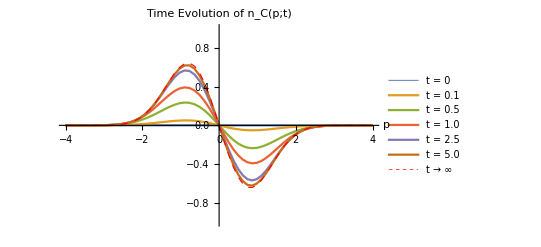

```mathematica
p4=Plot[{nc[p,Tdomain[[1]]],nc[p,Tdomain[[3]]],nc[p,Tdomain[[5]]],nc[p,Tdomain[[7]]],nc[p,Tdomain[[10]]],nc[p,Tdomain[[12]]],Subscript[n, C][p]},{p,-4,4},
PlotStyle->{{Default,Thickness[.004]},Default,Default,Default,Default,Default,{Red,Dashed,Thickness[.002]}},
PlotLegends->{"t = 0","t = 0.1","t = 0.5","t = 1.0","t = 2.5","t = 5.0","t → ∞"},
PlotRange->{-1.0,1.0},PlotPoints->5,MaxRecursion->4,
PlotLabel->Style["Time Evolution of n_C(p;t)",Bold,18],AxesLabel->{Style["p",15]},
TicksStyle->Directive["Label", 12],
ImageSize->Scaled[0.6]]
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\TimeEvolutionNC.png",p4];
```

#### Wave Function with Phase Difference θ

Now we will look at the answering the same questions but instead with a wave function where one of the terms has a complex phase factor ℯ^iθ where θ is a constant  ψ = 1/(√2)  (ψ_F χ_S + ψ_B χ_T ℯ^iθ)

#### Real Space Density Profile

We can calculate that the coupled term in the real space density profile will differ only by a factor of  cos(θ), allowing us to reuse our result from before

```mathematica
Manipulate[Plot[{Subscript[ns, F][x],0.5*(Subscript[ns, F][x] + Cos[θ]Subscript[ns, C][x]),0.5*(Subscript[ns, F][x] - Cos[θ]Subscript[ns, C][x])},{x,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Real Space Density Profile n_(σ, θ)(x)",Bold,16],PlotLegends->{"n_F(x)","σ = 1/2","σ = -1/2"},AxesLabel->{"x"}],{θ,0,2π}]
```

Let’s create a gif of this

```mathematica
pts=20;
Δ=1/(pts-1);
ThetaDomain=2π*Table[Δ*j,{j,0,1/Δ}];
frame[i_]:=Show[Plot[{Subscript[ns, F][x],0.5*(Subscript[ns, F][x] + Cos[ThetaDomain[[i]]]Subscript[ns, C][x]),0.5*(Subscript[ns, F][x] - Cos[ThetaDomain[[i]]]Subscript[ns, C][x])},{x,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.6],PlotLabel->Style["Real Space Density Profile n_(σ, θ)(x)",Bold,20],PlotLegends->{"n_F(x)","σ = 1/2","σ = -1/2"},AxesLabel->{Style["x",17]},TicksStyle->Directive["Label", 15]],
Graphics[Style[Text[StringForm["θ = ``",ThetaDomain[[i]]//N],{3,0.7},{0,0}],17]]];
frames=Table[frame[i],{i,1,Length[ThetaDomain]}];
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\ThetaEvolutionRSDP.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .12,ImageSize->Scaled[0.8]];
```

#### Momentum Space Density Profile (t = 0)

```mathematica
ncTheta0[p_]:=ncTheta0[p]=Round[NIntegrate[ⅇ^(-1/2 (p-ⅈ w) (p+3 ⅈ w)) √π (2 (p^2+w^2) (DawsonF[(p-ⅈ w)/(√2)]+ⅇ^(2 ⅈ p w) DawsonF[(p+ⅈ w)/(√2)])-2 √2 ⅇ^(ⅈ p w) (p Cos[p w]+w Sin[p w])),{w,-Infinity,Infinity}],10^-5]//N
ncTheta[p_,θ_]:=(-2Sin[θ])/π^2 ncTheta0[p];
nSigma[p_,θ_]:=0.25*(Subscript[n, F][p] + Subscript[n, B][p]+ncTheta[p,θ]);
pts=70;
Δ=1/(pts-1);
PDomain=8*Table[Δ*j,{j,0,1/Δ}]-4;
PPnf={#,Subscript[n, F][#]}&/@PDomain;
```

```mathematica
Manipulate[ListLinePlot[{PPnf,{#,nSigma[#,θ]}&/@PDomain,{#,nSigma[#,θ+π]}&/@PDomain},
PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},
ImageSize->Scaled[0.5],PlotLabel->Style["Momentum Space Density Profile n_(σ, θ)(p)",Bold,16],
PlotLegends->{"n_F(p)","σ = 1/2","σ = -1/2"},AxesLabel->{"p"}],{θ,0,2π}]
```

Again we can create a gif

```mathematica
pts=70;
Δ=1/(pts-1);
ThetaDomain=2π*Table[Δ*j,{j,0,1/Δ}];
frame[i_]:=Show[ListLinePlot[{PPnf,{#,nSigma[#,ThetaDomain[[i]]]}&/@PDomain,{#,nSigma[#,ThetaDomain[[i]]+π]}&/@PDomain},
PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},
ImageSize->Scaled[0.5],PlotLabel->Style["Momentum Space Density Profile n_(σ, θ)(p)",Bold,16],
PlotLegends->{"n_F(p)","σ = 1/2","σ = -1/2"},AxesLabel->{"p"}],
Graphics[Style[Text[StringForm["θ = ``",ThetaDomain[[i]]//N],{3,0.7},{0,0}],17]]];
frames=Table[frame[i],{i,1,Length[ThetaDomain]}];
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\ThetaEvolutionMSDP.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .15,ImageSize->Scaled[0.8]];
```

#### Momentum Space Density Profile Dynamical Fermionization (t → ∞)

Now we consider what the MSDP looks like after the trapping potential has been turned off. We find that it maintains the same behavior as the RSDP even as θ changes

```mathematica
Manipulate[Plot[{Subscript[n, F][p],0.5*(Subscript[n, F][p] + Cos[θ]Subscript[n, C][p]),0.5*(Subscript[ns, F][p] - Cos[θ]Subscript[n, C][p])},{p,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.5],PlotLabel->Style["Momentum Space Density Profile - Dynamical Fermionization n_(σ, θ)(p) as t → ∞",Bold,16],PlotLegends->{"n_F(p)","σ = 1/2","σ = -1/2"},AxesLabel->{"p"}],{θ,0,2π}]
```

```mathematica
pts=70;
Δ=1/(pts-1);
ThetaDomain=2π*Table[Δ*j,{j,0,1/Δ}];
frame[i_]:=Show[Plot[{Subscript[n, F][p],0.5*(Subscript[n, F][p] + Cos[ThetaDomain[[i]]]Subscript[n, C][p]),0.5*(Subscript[ns, F][p] - Cos[ThetaDomain[[i]]]Subscript[n, C][p])},{p,-4,4},PlotStyle->{{Red,Dashed,Thickness[.003]},{Darker[Blue],Opacity[0.7],Thickness[.003]},{Orange,Opacity[0.9],Thickness[.003]}},ImageSize->Scaled[0.6],PlotLabel->Style["Momentum Space Density Profile - Dynamical Fermionization n_(σ, θ)(p) as t → ∞",Bold,16],PlotLegends->{"n_F(p)","σ = 1/2","σ = -1/2"},AxesLabel->{Style["p",17]},TicksStyle->Directive["Label", 15]],
Graphics[Style[Text[StringForm["θ = ``",ThetaDomain[[i]]//N],{3,0.6},{0,0}],17]]];
frames=Table[frame[i],{i,1,Length[ThetaDomain]}];
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\ThetaEvolutionMSDP-DF.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .15,ImageSize->Scaled[0.8]];
```

#### Full Time Evolution of MSDP

Here we calculate a gif of the full time evolution of the MSDP for a few representative thetas
Recall that the full expression for the time dependent MSDP looks like

n_σ(p;t) =  1/2  ( n_B(p;t) + n_F(p;t) ) S_1 + n_C(p; t) S_2

```mathematica
Subscript[n, B][p_,t_] :=Subscript[n, B][p,t]= b[t]/π NIntegrate[Cos[b[t]*p(x-y) + (b[t]b'[t])/2(y^2-x^2)]Subscript[ρ, B][x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity},Method->"CartesianRule",AccuracyGoal->4];
Subscript[ρ, C][x_,y_]=Integrate[E^(-1/2(x^2+y^2))E^(-w^2)(w-x)Abs[w-y],{w,-Infinity,Infinity},Assumptions->{Im[x]==0,Im[y]==0}]//FullSimplify;
ncCosTheta[p_,t_]:=ncCosTheta[p,t]=NIntegrate[Cos[b[t]*p(x-y)+b[t]*b'[t]/2*(y^2-x^2)]Subscript[ρ, C][x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity},Method->"CartesianRule",AccuracyGoal->4];
ncSinTheta[p_,t_]:=ncSinTheta[p,t]=NIntegrate[Sin[b[t]*p(x-y)+b[t]*b'[t]/2*(y^2-x^2)]Subscript[ρ, C][x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity},Method->"CartesianRule",AccuracyGoal->4];
Subscript[n, C][p_,t_,θ_]:= b[t]/π^2(Cos[θ]*ncCosTheta[p,t]-Sin[θ]ncSinTheta[p,t])
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

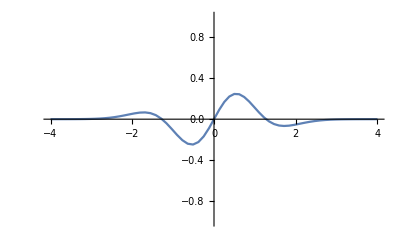
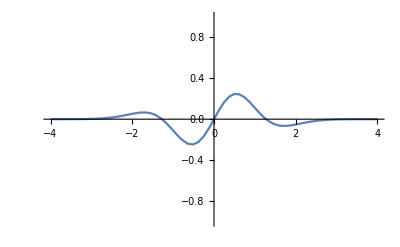
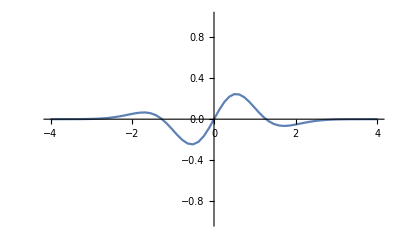
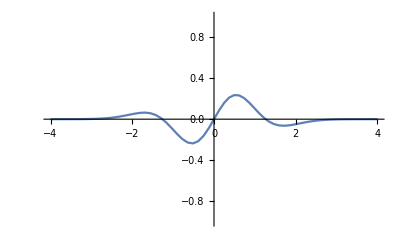
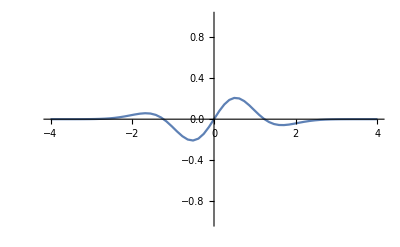
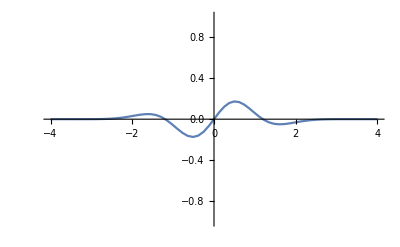
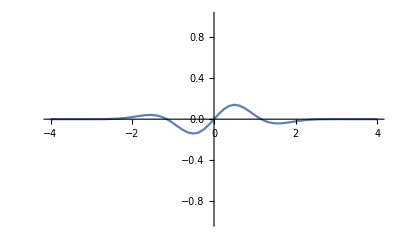
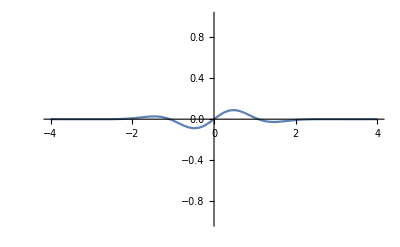

```mathematica
Tdomain={0.0,.05,.1,0.25,0.5,0.75,1.0,1.5, 2.0,2.5, 3.0,5.0, 7.0,9.0,11.0,13.0};
Plot[Subscript[n, B][p,Tdomain[[#]]],{p,-4,4},PlotRange->{0,1.2},PlotPoints->5,MaxRecursion->4]&/@Table[i,{i,1,Length[Tdomain]}];
Plot[{ncCosTheta[p,Tdomain[[#]]],ncSinTheta[p,Tdomain[[#]]]},{p,-4,4},PlotRange->{-2.5,2.5},PlotPoints->5,MaxRecursion->4]&/@Table[i,{i,1,Length[Tdomain]}];
Plot[Subscript[n, C][p,Tdomain[[#]],π/2],{p,-4,4},PlotRange->{-1,1},PlotPoints->5,MaxRecursion->4]&/@Table[i,{i,1,Length[Tdomain]}]
```

```mathematica
frame[i_]:=Show[Plot[{1/4(Subscript[n, B][p,Tdomain[[i]]]+Subscript[n, F][p])+1/2 Subscript[n, C][p,Tdomain[[i]],0],1/4(Subscript[n, B][p,Tdomain[[i]]]+Subscript[n, F][p])-1/2 Subscript[n, C][p,Tdomain[[i]],0],Subscript[n, F][p]},{p,-4,4},PlotStyle->{{Default,Thickness[0.003]}, {Default,Thickness[0.003]},{Red,Dashed,Thickness[0.003]}},TicksStyle->Directive["Label", 15], 
PlotRange->{0,1},PlotPoints->5,MaxRecursion->4,
PlotLabel->Style["Time Evolution of n_σ(p;t)",Bold,20],AxesLabel->{Style["p",17]},
PlotLegends->{"σ = 1/2","σ = -1/2","n_F(p)"}, ImageSize->Scaled[0.6]],
Graphics[Style[Text[StringForm["t = ``",Tdomain[[i]]],{3,0.7},{0,0}],17]]];
frames=Table[frame[i],{i,1,Length[Tdomain]}];
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\MSDPTimeEvolutionDF.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .25];
```

```mathematica
Pdomain=Range[19,22,1];
Tdomain = {0,0.25,.5,0.75,1,1.5,2,3,4};
Ρ[x_,y_]= 1/2*Integrate[Conjugate[Subscript[ψ, F][x,w,0]+Subscript[ψ, B][x,w,0]]*(Subscript[ψ, F][y,w,0]+Subscript[ψ, B][y,w,0]),{w,-Infinity, Infinity},Assumptions->{Im[x]==0,Im[y]==0}]//FullSimplify
```

1/2 (Piecewise[{{(ⅇ^(1/2 (-3 x^2-y^2)) (-2 y+ⅇ^(x^2) √π (1+2 x y) Erfc[x]))/π, x≥y}, {(ⅇ^(1/2 (-x^2-3 y^2)) (-2 x+ⅇ^(y^2) √π (1+2 x y) Erfc[y]))/π, True}}])

```mathematica
ℕ[p_,t_]:=ℕ[p,t]=b[t]/(2π)Re[NIntegrate[Exp[I*b[t]*p(x-y) + I(b[t]b'[t])/2(y^2-x^2)]Ρ[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity},Method->"CartesianRule",AccuracyGoal->13,PrecisionGoal->13]];
```

```mathematica
(* Set interopolation functions for various points in time *)
Subscript[dataSet, m_]:=Subscript[dataSet, m]=ℕ[Pdomain,Tdomain[[m]]]*Pdomain^4;
Do[Subscript[dataSet, i]=Subscript[dataSet, i],{i,1,Length[Tdomain]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(*Clear[ℕ]
Subscript[dataSet, 1]=.*)
```

```mathematica
SubMinus[Ρ][x_,y_]= 1/2*Integrate[Conjugate[Subscript[ψ, F][x,w,0]+-Subscript[ψ, B][x,w,0]]*(Subscript[ψ, F][y,w,0]-Subscript[ψ, B][y,w,0]),{w,-Infinity, Infinity},Assumptions->{Im[x]==0,Im[y]==0}]//FullSimplify
SubMinus[ℕ][p_,t_]:=SubMinus[ℕ][p,t]=b[t]/(2π)Re[NIntegrate[Exp[I*b[t]*p(x-y) + I(b[t]b'[t])/2(y^2-x^2)]Ρ[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity},Method->"CartesianRule",AccuracyGoal->13,PrecisionGoal->13]];
(* Set interopolation functions for various points in time *)
Subscript[dataSetMinus, m_]:=Subscript[dataSetMinus, m]=SubMinus[ℕ][Pdomain,Tdomain[[m]]]*Pdomain^4;
Do[Subscript[dataSetMinus, i]=Subscript[dataSetMinus, i],{i,1,Length[Tdomain]}]
```

1/2 (Piecewise[{{(ⅇ^(1/2 (-3 x^2-y^2)) (2 y+ⅇ^(x^2) √π (1+2 x y) (1+Erf[x])))/π, x<y}, {(ⅇ^(1/2 (-x^2-3 y^2)) (2 x+ⅇ^(y^2) √π (1+2 x y) (1+Erf[y])))/π, True}}])

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(* Prepare domains and ranges for extracting the coefficient*)
CoeffDep={};
Do[CoeffDep=Append[CoeffDep,Mean[Subscript[dataSet, i]]],{i,1,Length[Tdomain]}]
CoeffDepMinus={};
Do[CoeffDepMinus=Append[CoeffDepMinus,Mean[Subscript[dataSet, i]]],{i,1,Length[Tdomain]}]
SubPlus[𝒞]=Interpolation[Thread[{Tdomain,CoeffDep}]];
SubMinus[𝒞]=Interpolation[Thread[{Tdomain,CoeffDepMinus}]];
p9=Plot[{SubPlus[𝒞][t]/SubPlus[𝒞][0],SubMinus[𝒞][t]/SubMinus[𝒞][0],b[t]^(-3)},{t,0,4},PlotLabel->Style["Time Dependence of Momentum Tail Coefficient n_σ(p;t)",Bold,16],AxesLabel->{"Time (t)"},PlotLegends->"Expressions",ImageSize->Scaled[.5],PlotStyle->{Directive[Dashing[{0.005,0.05}],Thickness[0.02]], {Default, Opacity[1.0]}, {Default,Dashing[Medium],Thickness[0.007]}}]
Export["C:\\Users\\tskar\\Documents\\PhysicsResearch\\UltraColdAtoms\\Plots\\SpinorTanContactTimeDependence.png",p9]
```

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

-Graphics-

C:\Users\tskar\Documents\PhysicsResearch\UltraColdAtoms\Plots\SpinorTanContactTimeDependence.png